# SAE S4.03 : Programmation haut niveau

## Sujet du projet : Classification de tumeurs

Dans le cadre de cette SAE, j’ai choisi d’étudier la classification de tumeurs mammaires en deux catégories : bénignes ou malignes. Ce projet s’articule en deux parties complémentaires, chacune basée sur une source de données issue de la plateforme Kaggle.

### Première partie : Analyse exploratoire des données

La première partie s’appuie sur un fichier CSV contenant 32 variables, dont 30 sont quantitatives (par exemple : le rayon moyen des tumeurs, leur texture, leur surface, etc.). Cette section a pour objectif de réaliser une analyse exploratoire des données (EDA), suivie d’une classification supervisée à l’aide d’algorithmes de machine learning classiques (comme la régression logistique ou les forêts aléatoires), afin de déterminer les variables les plus discriminantes dans la détection de tumeurs malignes.

Objectif de la première partie :

Importer les données

Visualiser la répartition des tumeurs

Analyser les variables

Sélectionner les variables pertinentes

Régression sur les variables discriminantes

Modèle de machine learning ( régression logistique )

### Deuxième partie : Développement d’un modèle de Deep Learning

La seconde partie repose sur un jeu d’images médicales, également issu de Kaggle, représentant des clichés IRM de tumeurs cérébrales. L’objectif est ici de développer un modèle de deep learning, plus précisément un réseau de neurones convolutif (CNN), capable de classifier automatiquement les tumeurs à partir de leurs images, en exploitant les capacités d’apprentissage profond pour la reconnaissance visuelle.

Objectif de la deuxième partie :

Importer les images

Créer un jeu de données utilisable

Choisir et configurer un modèle de deep learning

Entraîner le modèle

Évaluer le modèle

(Créer une interface de test)

Ainsi, ce projet permet d’explorer deux approches complémentaires de la classification : l’une fondée sur des variables numériques tabulaires, l’autre sur des images.

## Première partie : Analyse exploratoire des données

### 1) Import du fichier CSV

```mathematica
texte = Import["C:\\Users\\rabah\\OneDrive\\Bureau\\BUT SD\\BUT1\\SAE_203\\data.csv", "Text"];

lignes = StringSplit[texte, "\n"];
data = Table[StringSplit[ligne,";"],{ligne,lignes}];

dataset = Dataset[data, HeaderBackground->Blue, Background->{{{LightBlue, White}}}]
```

### 2) Visualisation de la répartition des tumeurs

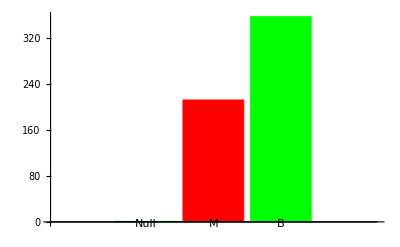

```mathematica
BarChart[Counts[data[[All,2]]], ChartStyle->{Green, Red}, ChartLabels->{"Null","M","B"}]
```

### 3) Analyse des variables

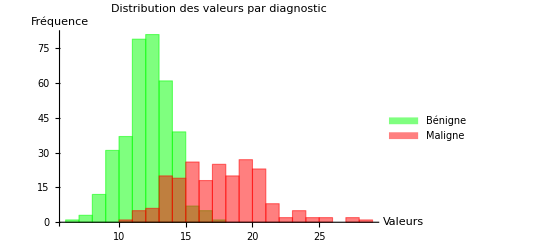

```mathematica
(*Supposons que la première ligne est l'en-tête*)
data=Rest[data]; (*Supprime l'en-tête*)
benigne=Select[data,#[[2]]=="B"&][[All,3]];(*Tumeurs bénignes*)
maligne=Select[data,#[[2]]=="M"&][[All,3]]; (*Tumeurs malignes*)

benigne=ToExpression[benigne]; (*conversion des caractère*)
maligne=ToExpression[maligne];
Histogram[
{benigne,maligne},ChartStyle->{Green,Red},PlotLabel->"Distribution des valeurs par diagnostic",AxesLabel->{"Valeurs","Fréquence"},ChartLegends->{"Bénigne","Maligne"}
]
```

L’histogramme montre que les diagnostics bénins (en vert) sont concentrés autour de 12-13, tandis que les diagnostics malins (en rouge) couvrent des valeurs plus élevées, entre 15 et 20. Cette séparation est nette.

Afin de déterminer quelles variables sont discriminantes ou non pour notre classification, nous allons simplement afficher les histogrammes pour chaque variables moyenne afin  de pouvoir identifier visuellement celles qui montrent une nette distinction entre les deux classes, et ainsi sélectionner les variables les plus pertinentes pour notre modèle de classification. Cette approche exploratoire permet de mettre en évidence les variables discriminantes de manière intuitive avant d’approfondir l’analyse avec des méthodes quantitatives plus robustes, si nécessaire.

### 4) Selection des variables discriminantes

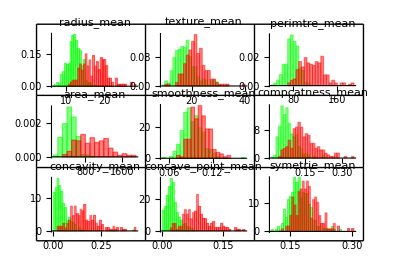

```mathematica
colonne={"radius_mean","texture_mean","perimtre_mean","area_mean","smoothness_mean","compcatness_mean","concavity_mean","concave_point_mean","symetrie_mean","fractal_dimension_mean"}; (*variables pertinentes*)

GraphicsGrid[
Partition[
Table[
benigne=Select[data,#[[2]]=="B"&][[All,col]];
maligne=Select[data,#[[2]]=="M"&][[All,col]];
benigne=ToExpression[benigne];
maligne=ToExpression[maligne];
Histogram[
{benigne,maligne},30,"PDF",ChartStyle->{Green,Red},PlotLabel->colonne[[col-2]]],{col,3,11}],UpTo[3]],Frame->All
]
```

Ces histogrammes montrent comment les variables sont distribuées dans deux catégories distinctes. La discrimination des variables est possible parce que certaines d’entre elles présentent une séparation visuelle évidente entre les deux couleurs (vert et rouge), représentant les deux groupes. Par exemple, lorsque les distributions ont peu de chevauchement, cela suggère que ces variables peuvent efficacement différencier les deux catégories. Plus précisément, les variables avec des différences marquées dans les pics ou les plages de valeurs offrent des indices puissants pour distinguer les diagnostics. C’est grâce à ces séparations visibles qu’on peut identifier les variables les plus discriminantes sans analyse supplémentaire.

### 5) Régression sur les variables discriminantes

```mathematica
colonneDeterminantes={"radius_mean","perimeter_mean","area_mean","concavity_mean","concave_points_mean"};
DynamicModule[{varX=1,varY=2},Column[{Row[{"Variable X: ",PopupMenu[Dynamic[varX],Range[Length[colonneDeterminantes]],Dynamic[colonneDeterminantes[[#]]]&],Spacer[20],"Variable Y: ",PopupMenu[Dynamic[varY],Range[Length[colonneDeterminantes]],Dynamic[colonneDeterminantes[[#]]]&]}],Dynamic[benigne=Select[data,#[[2]]=="B"&][[All,varX+2]];
maligne=Select[data,#[[2]]=="M"&][[All,varX+2]];
benigneY=Select[data,#[[2]]=="B"&][[All,varY+2]];
maligneY=Select[data,#[[2]]=="M"&][[All,varY+2]];
benigne=ToExpression[benigne];
maligne=ToExpression[maligne];
benigneY=ToExpression[benigneY];
maligneY=ToExpression[maligneY];
(*Calcul du coefficient de corrélation pour les deux variables*)
correlation=Correlation[Join[benigne,maligne],Join[benigneY,maligneY]];
Print["Correlation: ",correlation];
(*Ajustement linéaire*)
linearModel=LinearModelFit[Transpose[{Join[benigne,maligne],Join[benigneY,maligneY]}],x,x];
Column[
{Show[ListPlot[{Transpose[{benigne,benigneY}],Transpose[{maligne,maligneY}]},PlotStyle->{Green,Red},PlotLabel->colonneDeterminantes[[varX]]<>" vs "<>colonneDeterminantes[[varY]],AxesLabel->{colonneDeterminantes[[varX]],colonneDeterminantes[[varY]]}],Plot[linearModel[x],{x,Min[Join[benigne,maligne]],Max[Join[benigne,maligne]]},PlotStyle->Blue]],Text[
Style["Coefficient de corrélation : "<>ToString[correlation],Bold]]
}
]
]
}
]
]
```

Voici une interface permettant à l’utilisateur de sélectionner deux variables afin d’afficher leur nuage de points. En plus de cette visualisation, une courbe de régression linéaire est tracée pour mieux mettre en évidence la tendance entre les deux variables. Le coefficient de corrélation est également calculé afin d’évaluer la force et la direction de leur relation.

### 6) Modèle de Machine Learning ( Random Forest )

#### 6.1) pré-traitement des données

```mathematica
colonneIndices={3,5,6,7,9}; 
features=data[[All,colonneIndices]]; 
labelsRaw=data[[All,2]]; 
labels=If[#=="B",0,1]&/@labelsRaw;
SeedRandom[42];
shuffledData=RandomSample[Transpose[{features,labels}]]; 
trainingData=shuffledData[[1;;Round[0.8*Length[shuffledData]]]];
testData=shuffledData[[Round[0.8*Length[shuffledData]]+1;;]];

trainingFeatures=trainingData[[All,1]];
trainingLabels=trainingData[[All,2]];
testFeatures=testData[[All,1]];
testLabels=testData[[All,2]];
```

Dans cette première partie du pré-traitement des données nous allons juste faire un tirage aléatoire pour nos 80% de données entraînées et 20% des données testées pour notre modèle.

#### 6.2) Jeu d’entraînement pour les données de d’entraînement et de test

```mathematica
trainingSet=MapThread[Rule,{trainingFeatures,trainingLabels}];
testSet=MapThread[Rule,{testFeatures,testLabels}];
```

Cette partie du code prend les données d’entraînement et de test, qui sont sous forme de listes de caractéristiques et de labels, et les associe sous forme de paires clé-valeur.

#### 6.3) Entraînement avec un le modèle Random Forest

```mathematica
classifierRF=Classify[trainingSet,Method->"RandomForest",PerformanceGoal->"Quality"];
```

Ici pour notre modèle nous avons décider d’utiliser un Random Forest. Pourquoi ? Pour plusieurs raisons :

Nombre de lignes : 500

Limite le risque de sur-apprentissage

Tolérance au bruit

Pas besoin de réglages complexe

Rapide à entraîner

#### 6.4) Calcul du Accuracy sur les données d’entraînement

```mathematica
accuracyTrainRF=ClassifierMeasurements[classifierRF,trainingSet,"Accuracy"];
Print["Accuracy (Entraînement, Random Forest) : ",accuracyTrainRF];
```

Accuracy (Entraînement, Random Forest) : 0.903297

#### 6.5) Calcul du Accuracy sur les données de test

```mathematica
accuracyTestRF=ClassifierMeasurements[classifierRF,testSet,"Accuracy"];
Print["Accuracy (Test, Random Forest) : ",accuracyTestRF];
```

Accuracy (Test, Random Forest) : 0.859649

Comme nous pouvons le constater ici notre modèle de Random Forest est en Over-fitting, c’est-à-dire que l’Accuracy faite sur les données de d’entraînement sont supérieures à l’Accuracy calculée sur les données de tests

#### 6.6) Matrice de confusion du modèle sur les données d’entraînement

```mathematica
confusionMatrixTrainRF=ClassifierMeasurements[classifierRF,trainingSet,"ConfusionMatrix"];
```

```mathematica
Print["Matrice de confusion (Entraînement, Random Forest) :",Grid[confusionMatrixTrainRF,Frame->All,PlotLabel->Style["Matrice : Entraînement - Random Forest",Bold,16],Spacings->{2,2},ItemStyle->Directive[Bold,Large]]];
```

Matrice de confusion (Entraînement, Random Forest) :277 | 5 | 0
39 | 134 | 0

#### 6.7) Matrice de confusion du modèle sur les données de test

```mathematica
(*Matrice de confusion pour Random Forest sur données de test*)
confusionMatrixTestRF=ClassifierMeasurements[classifierRF,testSet,"ConfusionMatrix"];
Print["Matrice de confusion (Test, Random Forest) :",Grid[confusionMatrixTestRF,Frame->All,PlotLabel->Style["Matrice : Test - Random Forest",Bold,16],Spacings->{2,2},ItemStyle->Directive[Bold,Large]]];
```

Matrice de confusion (Test, Random Forest) :72 | 3 | 0
13 | 26 | 0

Comme on peut le voir ici, nos deux matrices de confusion montrent un nombre élevé d’erreurs de première espèce : un grand nombre de patients atteints de tumeurs malignes sont identifiés à tort comme ayant des tumeurs bénignes. Ce type d’erreur est particulièrement préoccupant dans un modèle de classification, car il implique que des cas graves sont sous-estimés. Dans un contexte médical, il est crucial de minimiser ce type d’erreur pour éviter des retards dans le traitement des patients. Par conséquent, ce modèle doit être amélioré, en ajustant par exemple ses seuils de décision, ou en explorant des techniques pour augmenter la précision de la classification des tumeurs malignes.

## Deuxième partie : Développement d’un modèle de Deep Learning

### 1) Import des images

```mathematica
SetDirectory["C:\\Users\\rabah\\OneDrive\\Bureau\\BUT SD\\BUT2\\S4\\Programmation haut niveau\\Projet SAE\\brain_tumor_dataset"];

malignes=FileNames["*.jpg","yes",1];
benignes=FileNames["*.jpg","no",1];

Print["Images malignes : ",Length[malignes]];
Print["Images bénignes : ",Length[benignes]];
```

Images malignes : 154

Images bénignes : 91

Les images des tumeurs sont enregistrées dans un dossier contenant deux autres dossier intitulé “no” et “yes”, où le dossier “no” va contenir toutes les tumeurs bénignes et le dossier “yes” va contenir les tumeurs malignes.  J’initialise simplement les chemins où les images se trouvent pour les deux types de tumeurs.

### 2) Création du jeu de données avec labels numériques

```mathematica
data=Join[Map[Function[f,<|"Image"->Import[f],"Label"->2|>],malignes],Map[Function[f,<|"Image"->Import[f],"Label"->1|>],benignes]];
```

Création du jeu de données avec les labels numériques afin de toper toutes les données et les rassembler dans une même variable “data”, les tumeurs bénignes sont topées 1 et les tumeurs malignes sont topées 2. C’est à partir de ce nouveau jeu de d’images que nous pourrons redimensionner nos images afin de faciliter l’entraînement au modèle.

### 3) Prétraitement ( nettoyage et redimensionnement des images )

```mathematica
processedData=Select[data,ImageQ[#Image]&];
processedData=processedData/. <|"Image"->img_,"Label"->lbl_|>:><|"Image"->ImageResize[img,{224,224}],"Label"->lbl|>;

Print["Total d'exemples après nettoyage : ",Length[processedData]];
```

Total d'exemples après nettoyage : 245

Ce bloc de code permet de nettoyer les données en filtrant uniquement les images valides, de redimensionner toutes les images à 224×224 pixels afin de les adapter à l’entrée du modèle de deep learning.

### 4) Séparation des données d’entraînement / test

```mathematica
(*Étape 4:Séparer données entraînement/validation*)
n=Length[processedData];
SeedRandom[42];
shuffled=RandomSample[processedData];
{trainData,valData}=TakeDrop[shuffled,Round[0.8*n]];

Print["Train set : ",Length[trainData]," | Val set : ",Length[valData]];
```

Train set : 196 | Val set : 49

Ce bloc de code permet de sélectionner aléatoirement les valeurs qui vont être utilisées pour l’entraînement et les phases de tests du modèle.

### 5) Définition du modèle

```mathematica
baseNet=NetModel["EfficientNet Trained on ImageNet"];
net=NetChain[{baseNet,LinearLayer[2],SoftmaxLayer[]},"Input"->NetEncoder[{"Image",{224,224},ColorSpace->"RGB"}],"Output"->NetDecoder[{"Class",{1,2}}]];

trainExamples=Map[<|"Input"->#Image,"Output"->#Label|>&,trainData];
valExamples=Map[<|"Input"->#Image,"Output"->#Label|>&,valData];
```

Pour entraîner notre modèle on utilise “EfficientNet” qui est un modèle de classification d’images pré entraîné sur image ImagNet, qui est un très grande base de données d’images,  on la récupère ici afin de réutiliser ses connaissances par transfert d’apprentissage et de ne pas repartir à 0. 

NetChain va assembler les couches du modèle . Elle utilise d’abord le modèle pré entraîné EfficientNet, qui sert ici de base pour extraire automatiquement des caractéristiques pertinentes à partir des images. À la suite de ce modèle, une couche linéaire à deux neurones est ajoutée pour produire deux scores, correspondant aux deux classes possibles dans la tâche de classification. Ces scores sont ensuite transformés en probabilités grâce à une couche Softmax, qui permet de déterminer la classe prédite avec une interprétation probabiliste. Le modèle est configuré pour recevoir en entrée des images de taille 224×224 pixels au format RGB, grâce à un encodeur d’images spécifié avec NetEncoder. Enfin, la sortie est définie comme une classe parmi deux possibles (1 ou 2), à l’aide d’un décodeur de type NetDecoder, ce qui permet à NetTrain d’interpréter correctement les prédictions pendant l’entraînement et l’évaluation.

Ce code reformate les données d’entraînement et de validation en exemples prêts à être utilisés par le modèle en associant chaque image à son étiquette sous la forme <|”Input” -> image, “Output” -> label|>, ce qui permet à NetTrain de comprendre clairement quelles sont les entrées du réseau et quelles sont les sorties attendues pour l’apprentissage.

### 6) Entraînement du modèle

```mathematica
trainedNet=NetTrain[net,trainExamples,ValidationSet->valExamples,BatchSize->16,MaxTrainingRounds->4,LossFunction->CrossEntropyLossLayer["Index"],TrainingProgressReporting->"Panel"];
```

Cette ligne entraîne le modèle net en utilisant les exemples d’entraînement trainExamples et les exemples de validation valExamples pour évaluer la performance du modèle pendant l’entraînement. L’entraînement est configuré avec une taille de lot de 16, ce qui signifie que le modèle traite 16 exemples à la fois avant de mettre à jour ses paramètres. Il est limité à 4 itérations sur l’ensemble des données (4 époques). La fonction de perte choisie est l’entropie croisée, qui est couramment utilisée pour les tâches de classification, et la mise à jour des poids se fait en fonction des indices des classes. Enfin, un panneau de progression est activé pour suivre l’avancement de l’entraînement en temps réel.

### 7) Evaluation du modèle

Précision sur les données d'entraînement : 0.897959

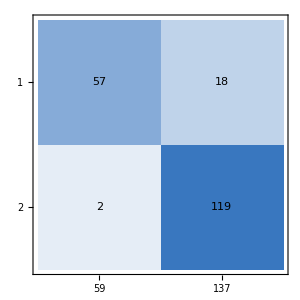
Matrice de confusion (données d'entraînement) : actual class | -Graphics-
 | predicted class

Précision sur les données de test : 0.877551

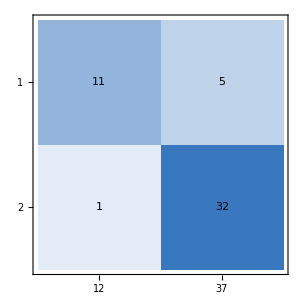
Matrice de confusion (données de test) : actual class | -Graphics-
 | predicted class

```mathematica
(*Précision et matrice de confusion sur les données d'entraînement*)
trainAccuracy=NetMeasurements[trainedNet,trainExamples,"Accuracy"];
Print["Précision sur les données d'entraînement : ",trainAccuracy];
Print["Matrice de confusion (données d'entraînement) : ",NetMeasurements[trainedNet,trainExamples,"ConfusionMatrixPlot"]];

(*Précision et matrice de confusion sur les données de test/\validation*)
testAccuracy=NetMeasurements[trainedNet,valExamples,"Accuracy"];
Print["Précision sur les données de test : ",testAccuracy];
Print["Matrice de confusion (données de test) : ",NetMeasurements[trainedNet,valExamples,"ConfusionMatrixPlot"]];
```

Comme dans notre premier modèle celui ci est en Over-fitting mais cette fois-ci les erreurs de premières espèces sont beaucoup moins importantes. Comme le montre notre matrice de confusion de test il n’y a qu’une personne qui a été classifiée comme une personne atteinte d’une tumeur bénigne alors qu’elle est maligne. Par conséquent, notre modèle de Deep Learning est plus efficace que celui de Machine Learning.

## Difficultés rencontrées

### Première partie : Analyse exploratoire des données

Modèle avec un trop grand overfitting

Trop d’erreurs de première espèce dans mon modèle

### Deuxième partie : Développement d’un modèle de Deep Learning

Mon modèle aurait pu être mieux entraîner si j’avais eu plus d’images

Mon pc n’est pas assez puissant pour pouvoir ajuster certains paramètre afin d’optimiser la précision de mon modèle

Mon interface utilisateur n’a pas ponctionnée